机器学习

本书到目前为止，当我们想让 Wolfram 语言做一些事情时，我们会写代码来告诉它到底该怎么做。但是，Wolfram 语言也被设定为能够使用机器学习的理念，通过观察例子来学习如何做。

我们将讨论如何自己训练语言。但首先让我们看看一些已经在大量实例上训练过的内置函数。

LanguageIdentify 接收文本片段，并识别它们使用的是什么人类语言。

确定每个短语所使用的语言：

```mathematica
LanguageIdentify[{ "thank you","merci","dar las gracias","感謝","благодарить"}]
```

{English,French,Spanish,Chinese,Russian}

Wolfram 语言也可以完成相当困难的“人工智能”任务，即识别图像是什么。

识别图像的内容：

```mathematica
ImageIdentify[-Graphics-]
```

cheetah

有一个通用的函数 Classify，它已经被示教了各种类型的分类。一个例子是对文本的“情感”进行分类。

乐观的文本被归类为具有积极的情绪：

```mathematica
Classify["Sentiment","I'm so excited to be programming"]
```

Positive

悲观的文本被归类为具有负面情绪：

```mathematica
Classify["Sentiment","math can be really hard"]
```

Negative

你也可以自己训练 Classify。下面是一个将手写数字分类为0或1的简单例子。你给 Classify 一个训练示例的集合，然后是一个特定的手写数字。然后它就会告诉你，你给的数字是0还是1。

通过训练实例，Classify 正确地识别了一个手写的0：

```mathematica
Classify[{-Graphics-->0,-Graphics-->1,-Graphics-->0,-Graphics-->1,-Graphics-->1,-Graphics-->0,-Graphics-->0,-Graphics-->1,-Graphics-->1,-Graphics-->0,-Graphics-->0,-Graphics-->0,-Graphics-->1,-Graphics-->0,-Graphics-->1,-Graphics-->0,-Graphics-->1,-Graphics-->1,-Graphics-->1},
-Graphics-]
```

0

为了了解这一点，并且因为它本身就很有用，让我们来谈谈 Nearest 这个函数，它可以找到列表中哪个元素与你提供的元素最接近。

找出列表中与22最接近的数字：

```mathematica
Nearest[{10,20,30,40,50,60,70,80},22]
```

{20}

找到最接近的三个数字：

```mathematica
Nearest[{10,20,30,40,50,60,70,80},22,3]
```

{20,30,10}

Nearest 也能找到最近的颜色：

在列表中找出与你给出的颜色最接近的3种颜色：

```mathematica
Nearest[{Hue[0.],Hue[0.05],Hue[0.1],Hue[0.15000000000000002],Hue[0.2],Hue[0.25],Hue[0.30000000000000004],Hue[0.35000000000000003],Hue[0.4],Hue[0.45],Hue[0.5],Hue[0.55],Hue[0.6000000000000001],Hue[0.65],Hue[0.7000000000000001],Hue[0.75],Hue[0.8]},RGBColor[0.8727094319714808, 0.9066617343162084, 0.09569669807641734],3]
```

{Hue[0.15000000000000002],Hue[0.2],Hue[0.25]}

它也适用于文字。

在单词列表中找出与 “good”最接近的10个单词。

```mathematica
Nearest[WordList[ ],"good",10]
```

{good,food,goad,god,gold,goo,goody,goof,goon,goop}

对图像来说也有一个近似的概念。虽然这远远不是全部，但这实际上是 ImageIdentify 所使用的部分内容。

与此相关的是识别文本(光学字符识别或 OCR)。让我们创建一个模糊的文本。

创建一个“hello”字样的图像，然后将其模糊化。

```mathematica
Blur[Rasterize[Style["hello",30]],3]
```

-Graphics-

TextRecognize 仍然可以识别其中的原始文本字符串。

识别图像中的文字：

```mathematica
TextRecognize[-Graphics-]
```

hello

如果文字变得太模糊， TextRecognize 就无法分辨它到底是什么—你可能也无法分辨。

生成一系列逐渐模糊的文本：

```mathematica
Table[Blur[Rasterize[Style["hello",15]],r],{r,0,4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

随着文字越来越模糊，TextRecognize 会出现错误，然后完全放弃：

```mathematica
Table[TextRecognize[Blur[Rasterize[Style["hello",15]],r]],{r,0,4}]
```

{hello,hello,hella,,}

如果我们逐步模糊猎豹的图片，也会发生类似的情况。当图片仍然相当清晰时，ImageIdentify 会正确地识别它是一只猎豹。但是当它变得太模糊时，ImageIdentify 开始认为它更有可能是一只狮子，最后最多只能猜测它是一张人的照片。

逐步模糊一张猎豹的照片：

```mathematica
Table[Blur[-Graphics-,r],{r,0,22,2}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

当图片变得过于模糊时，ImageIdentify 不再认为它是一只猎豹：

```mathematica
Table[ImageIdentify[Blur[-Graphics-,r]],{r,0,22,2}]
```

{cheetah,cheetah,cheetah,cheetah,lion,red wolf,domestic dog,musteline mammal,domestic dog,person,person,person}

ImageIdentify 通常只给出它认为最可能的识别。不过你可以告诉它，从最有可能的开始，给出一个可能的识别列表。下面是所有类别中的前10个最有可能的识别结果。

ImageIdentify 认为这可能是一只猎豹，但更可能是一只狮子，也可能是一只狗：

```mathematica
ImageIdentify[-Graphics-,All,10]
```

{lion,red wolf,cheetah,wildcat,domestic dog,striped hyena,pine marten,mountain lion,working dog,lynx}

当图像足够模糊时，ImageIdentify 对它可能是什么会产生一些疯狂的想法：

```mathematica
ImageIdentify[-Graphics-,All,10]
```

{person,domestic dog,edible fruit,hunting dog,cat,berry,terrier,wildcat,working dog,soft-finned fish}

在机器学习中，人们经常给予明确的训练，例如，“这是一只猎豹”，“这是一只狮子”。但人们也经常只是想在没有任何特定训练的情况下自动挑选出事物的类别。

开始做这件事的一个方法是，取一个事物的集合，比如说颜色，然后找到类似的簇。这可以用 FindClusters 来实现。

将相似颜色的“簇”收集到单独的列表中：

```mathematica
FindClusters[{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]}]
```

{{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]},{RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}]},{RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}]},{RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}]}}

你可以通过将每种颜色与列表中最相似的三种颜色连接起来，然后将这些连接做成一个图来获得不同的视角。在这个特定的例子中，最终有三个不相连的子图。

根据“颜色空间”中的接近程度，创建一个连接图：

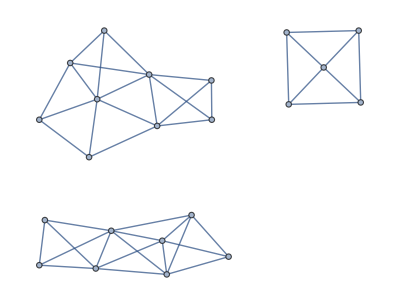

```mathematica
NearestNeighborGraph[{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]},3,VertexLabels->All]
```

树状图可以让你看到整个层次结构中什么靠近什么的。

将相近的颜色连续组合在一起：

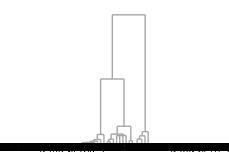

```mathematica
Dendrogram[{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]}]
```

当我们比较事物时，无论是颜色还是动物的图片，我们都可以考虑找出某些特征，让我们把它们区分开来。对于颜色来说，一个特征可能是颜色有多浅，或者它含有多少红色。对于动物图片，一个特征可能是动物看起来有多毛茸茸，或者它的耳朵有多尖。

在 Wolfram 语言中，FeatureSpacePlot 使用对象的集合，并试图找到它认为是“最佳”的区分特征，然后使用这些特征的值以一个图中定位对象。

FeatureSpacePlot 并不会明确说明它使用的是什么特征，实际上它们通常很难描述。但最终发生的情况是，FeatureSpacePlot 使具有类似特征的对象被画在附近。

FeatureSpacePlot 把类似的颜色放在附近：

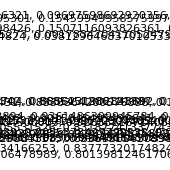

```mathematica
FeatureSpacePlot[{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]}]
```

如果使用完全随机挑选的100种颜色，那么 FeatureSpacePlot 将再次把它认为相似的颜色放在附近。

用 FeatureSpacePlot 排布的100种随机颜色：

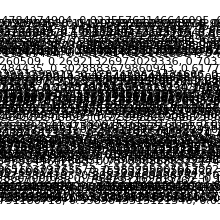

```mathematica
FeatureSpacePlot[RandomColor[100]]
```

让我们用字母的图像试试同样的事情：

为字母表中的每个字母创建一个光栅化图像：

```mathematica
Table[Rasterize[FromLetterNumber[n]],{n,26}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

FeatureSpacePlot 将使用这些图像的视觉特征来排列它们。其结果是，那些看起来相似—比如 y、v、e 和 c—的字母会邻近排列。

```mathematica
FeatureSpacePlot[Table[Rasterize[FromLetterNumber[n]],{n,26}]]
```

-Graphics-

下面是同样的事情，但现在有了猫、汽车和椅子的图片。FeatureSpacePlot 将立即把不同种类的事物分开。

FeatureSpacePlot 将不同种类的事物的照片排布得比较远：

```mathematica
FeatureSpacePlot[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

-Graphics-

词汇

LanguageIdentify[text] |   | 识别文本中使用的是哪种人类语言
ImageIdentify[image] |   | 识别图像中是什么对象
TextRecognize[text] |   | 从图像中识别文本(OCR)
Classify[training,data] |   | 根据给定的训练示例来分类数据
Nearest[list,item] |   | 查找列表中与给定项目最接近的元素
FindClusters[list] |   | 找出类似项目的簇
NearestNeighborGraph[list,n] |   | 将列表中的元素与它们的 n 个最近的邻居连接起来
Dendrogram[list] |   | 将项之间的关系创建为分层级的树状图
FeatureSpacePlot[list] |   | 在推断的“特征空间”中绘制列表中的元素

"共有 16 道习题"
"以及 7 道附加题" | "开始练习 »"

找出“ajatella”这个词来自哪种语言。»

| 期望输出： |  
  | "Finnish" |

将 ImageIdentify 应用于老虎的图像，用 ctrl= 来获得图像。»

| 期望输出： |  
  | "tiger" |

为一张老虎的图像制作一张图像识别的表，图像的模糊程度从 1 变化到 5。»

| 期望输出： |  
  | {"tiger","tiger","domestic cat","domestic cat","person"} |

对 “I’m so happy to be here” 这句话进行情绪分类。»

| 期望输出： |  
  | "Positive" |

在 WordList[ ] 中找出与 “happy” 最接近的10个词。»

| 期望输出： |  
  | {"happy","haply","harpy","nappy","sappy","apply","campy","choppy","guppy","hairy"} |

生成 20 个 1000 以内的随机数，并找出其中 3 个最接近 100 的数字。»

| 期望输出示例： |  
  | {94,91,133} |

生成一个包含 10 种随机颜色的列表，并找出其中 5 种最接近红色的颜色。»

| 期望输出示例： |  
  | {RGBColor[0.9132382296127133, 0.1052875704634939, 0.1081561232856334],RGBColor[0.9771026336083766, 0.363796063619348, 0.01077019070224905],RGBColor[0.9549993293169798, 0.21676827484502326, 0.2513102591499172],RGBColor[0.8483679553563124, 0.30385712208149696, 0.15484335046598763],RGBColor[0.9594790623807896, 0.5046051552943853, 0.18946774256928367]} |

在前 100 个数字的平方中，找出最接近 2000 的一个。»

| 期望输出： |  
  | 2025 |

找到与巴西(Brazil)国旗最近的 3 个欧洲国家的国旗。»

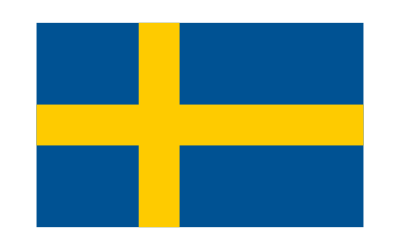
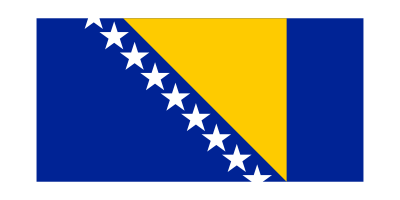
| 期望输出： |  
  | {-Graphics-,-Graphics-,-Graphics-} |

为 Table[Hue[h],{h,0,1,.05}] 中的每种颜色的 2 个最近的邻居创建一个图。»

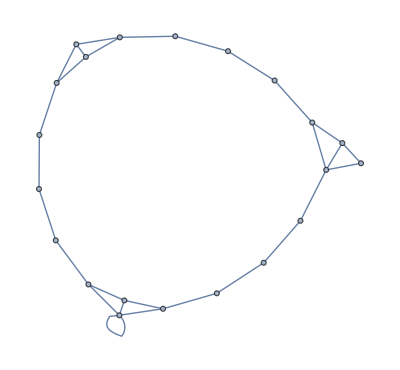
| 期望输出： |  
  | -Graphics- |

生成一个包含 100 个 100 以内的随机数的列表，创建列表中的每个数的 2 个最近的邻居的图。»

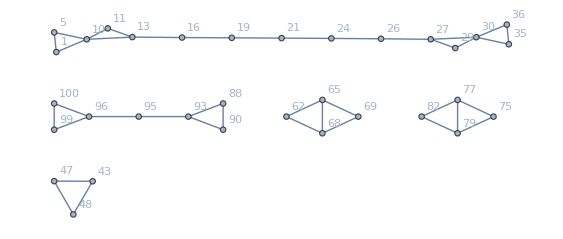
| 期望输出示例： |  
  | -Graphics- |

将亚洲国家的国旗按相似性进行分类。»

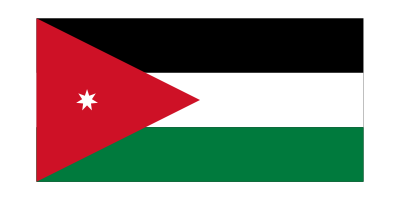
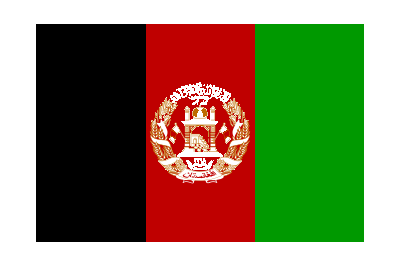
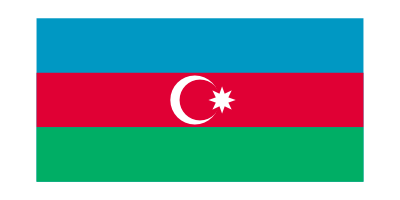
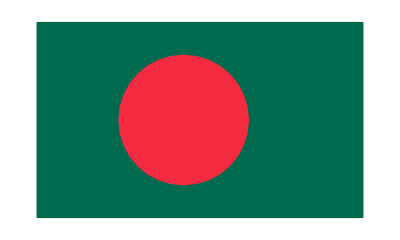
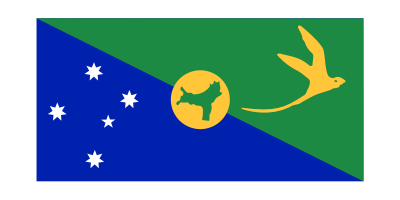
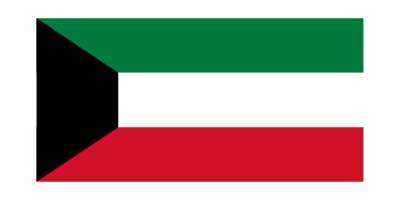
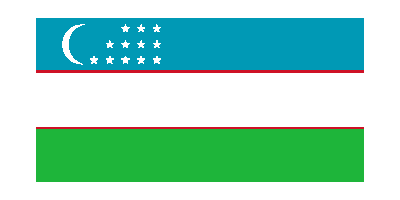
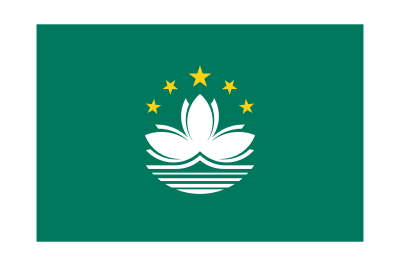

| 期望输出： |  
  | {{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}} |

为字母表中的每个字母创建大小为 20 的光栅图像，然后创建每个字母的 2 个最近的邻居的图。»

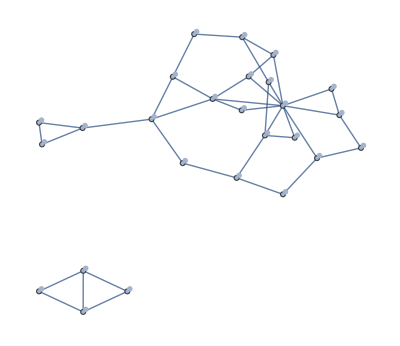
| 期望输出： |  
  | -Graphics- |

对尺寸为 50，模糊程度从 1 变化到 10 的 “hello” 的光栅化图像使用 TextRecognize，生成结果列表。»

| 期望输出： |  
  | {"hello","hello","hello","hello","hello","hello","hllo","","",""} |

为字母表中的前 10 个字母的图像创建一个树状图。»

| 期望输出： |  
  | -Graphics- |

为英文大写字母创建一个特征空间图。»

| 期望输出： |  
  | -Graphics- |

为一张埃菲尔铁塔(Eiffel Tower)的图片创建一个图像识别表，模糊程度从 1 变化到 5。»

| 期望输出： |  
  | {"Eiffel Tower","tower","tower","tower","device"} |

对维基百科上关于“happiness”的文章进行情绪分类。»

| 期望输出： |  
  | "Neutral" |

在列表 Table[Hue[h],{h,0,1,.05}] 中的颜色找出与粉红色最接近的 3 种颜色。»

| 期望输出： |  
  | {Hue[0.9500000000000001],Hue[0.9],Hue[0.05]} |

计算 i 和 j 在 500 以内的所有分数 i/j ，并找出最接近 pi 的 10 个分数。»

| 期望输出： |  
  | {355/113,377/120,333/106,399/127,311/99,421/134,443/141,289/92,465/148,487/155} |

生成一个包含 10 个 10 以内的随机数的列表，并为每个数的 3 个最近的邻居创建一个图。»

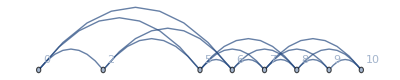
| 期望输出： |  
  | -Graphics- |

在 100 个随机颜色的列表中找到相似颜色的族群。»

| 期望输出： |  
  | {{RGBColor[0.8116438051434329, 0.8547919864863347, 0.7807710853793401],RGBColor[0.2983278570382957, 0.9907444932950316, 0.9284043344039434],RGBColor[0.18676117011450066, 0.5486089602170863, 0.04303247680226141],RGBColor[0.4044608902823441, 0.9788998961090443, 0.8108975624714536],RGBColor[0.5308001574813235, 0.9503472359039511, 0.8646083755834806],RGBColor[0.5926608241659339, 0.4671421812435703, 0.027570072930602985],RGBColor[0.49843743964638865, 0.7588128836239783, 0.6588996785867525],RGBColor[0.6788691428209239, 0.8865118691450595, 0.06859340947663295],RGBColor[0.3966954095359472, 0.9303983446364068, 0.27133513969525125],RGBColor[0.7496777159050012, 0.8414031368083361, 0.29000881481349006],RGBColor[0.1722869702422274, 0.42066881136044554, 0.18877704427888808],RGBColor[0.020568097401979735, 0.32843933224376776, 0.2578912775452169],RGBColor[0.4276762158276948, 0.9445301871184215, 0.6339408432442302],RGBColor[0.3449333805776824, 0.8214093187031501, 0.00535396147946221],RGBColor[0.9595114792486563, 0.9614567195621035, 0.09956803288245264],RGBColor[0.13927723404143122, 0.9837658758454813, 0.6275322853052734],RGBColor[0.4129872979782936, 0.599123151026224, 0.5563798982651478],RGBColor[0.5517409716001453, 0.7226268672047083, 0.04296745155978088],RGBColor[0.2471012449687613, 0.6622219052252245, 0.34136700529740893],RGBColor[0.00852878273374924, 0.7623891609381206, 0.495048201930645],RGBColor[0.410530117230961, 0.65951899493187, 0.31274019237510875],RGBColor[0.14914425266109754, 0.8632288046219025, 0.2165769996518021],RGBColor[0.5019554020533212, 0.5771425709059108, 0.4324648041012522],RGBColor[0.2375846642639532, 0.7953276430316651, 0.9346352336682711],RGBColor[0.5670638896981823, 0.30694748662903737, 0.07724772234151844],RGBColor[0.9836330486106633, 0.9337141420685637, 0.45110780147188234],RGBColor[0.548151102001315, 0.9273818734933321, 0.6138604019189067],RGBColor[0.08996343949980967, 0.7502285322367264, 0.7647837622874905],RGBColor[0.9554445238224603, 0.9118174885785313, 0.7586039763217882],RGBColor[0.12407876246761118, 0.8951986963374581, 0.405054951518828],RGBColor[0.3518853673765441, 0.6267881822227646, 0.01601455063963053],RGBColor[0.38175543134617906, 0.6109792496345561, 0.30321055377645356],RGBColor[0.5015968883258048, 0.9477341972992892, 0.7518749706067847],RGBColor[0.4853791041906068, 0.9983056811536988, 0.059586297674913524],RGBColor[0.39598681356054666, 0.5894657294683947, 0.2897133293523855],RGBColor[0.06510008212093177, 0.7580810151353965, 0.4838966525370989],RGBColor[0.02229677965825383, 0.35028891391213257, 0.0684550207396537],RGBColor[0.15578960479774717, 0.33156505911261824, 0.10795082362400787],RGBColor[0.9666406011133539, 0.6653552686335491, 0.5546554666254075],RGBColor[0.21832422216206182, 0.4452088456726624, 0.34195667187604584],RGBColor[0.4939446101923697, 0.31678858836269796, 0.11346988660388835],RGBColor[0.9566388456878347, 0.9651195544633302, 0.9076564789046491],RGBColor[0.4000855073593619, 0.39588066174906866, 0.1685452332949151],RGBColor[0.5700736595139675, 0.4069545472059297, 0.1981313907220874],RGBColor[0.16637070232988593, 0.6273450506223697, 0.6129198387249786],RGBColor[0.15217789308335927, 0.6805446503579162, 0.7536712821543405],RGBColor[0.011500166973726689, 0.9344737120630893, 0.41519231703372195],RGBColor[0.6487763190386047, 0.9218976224198998, 0.711816672844579],RGBColor[0.47327935747334204, 0.8834140175937308, 0.33245673464773584],RGBColor[0.25560515056407795, 0.8012401319897553, 0.15094027368448049],RGBColor[0.13360546814982577, 0.7871863239201633, 0.018599162734135977],RGBColor[0.38337417819768205, 0.4988952587556723, 0.08321860516969015],RGBColor[0.4181367040733106, 0.49313383402211364, 0.10167945128775124],RGBColor[0.4812053533680498, 0.873332380181423, 0.327028956990717],RGBColor[0.5269434582467774, 0.8294337802982428, 0.1734709900484559]},{RGBColor[0.37266534273681007, 0.38750269832660855, 0.3948182017762212],RGBColor[0.733606571264461, 0.4291909747287308, 0.4301886698173236],RGBColor[0.17707863410973768, 0.672607405954065, 0.8338273497920801],RGBColor[0.8745580077995285, 0.08910005366925322, 0.5820198361552016],RGBColor[0.9090294322469556, 0.2839329014344203, 0.5231271919589293],RGBColor[0.4864384781423896, 0.2590016473319656, 0.8939198034327294],RGBColor[0.2674220618976657, 0.5345197867819858, 0.7888815584252213],RGBColor[0.18736123677107708, 0.3952086052502788, 0.86460527303447],RGBColor[0.7776461280660796, 0.8643601244579295, 0.9944319426310919],RGBColor[0.10244743490058794, 0.1869170597224914, 0.6271170684614624],RGBColor[0.4573447796522936, 0.007181376876192136, 0.566195028583903],RGBColor[0.23258722219837846, 0.08344742427005825, 0.30644177688225716],RGBColor[0.711485166849398, 0.017375777675906035, 0.7454946682315056],RGBColor[0.31452599923983104, 0.6908103742720597, 0.9463506847311731],RGBColor[0.922559309792595, 0.2703946335791436, 0.09665543181913394],RGBColor[0.11122524183982829, 0.12772449779541217, 0.6139200516853858],RGBColor[0.6357194627252103, 0.15357943517679362, 0.860476954867391],RGBColor[0.4431832834876257, 0.18321465791748515, 0.7764518003586576],RGBColor[0.3553518860908462, 0.6443320866741731, 0.7499636864238166],RGBColor[0.8943854155561495, 0.03560200287351467, 0.16578917868909593],RGBColor[0.6672396717157738, 0.3586192991395154, 0.8976595916455246],RGBColor[0.37001635641206, 0.3047563933568622, 0.7684408201506054],RGBColor[0.38698691150966935, 0.10328204902950966, 0.8013210231747274],RGBColor[0.29215345853340424, 0.35497646703617836, 0.6346432521789236],RGBColor[0.9678407581110904, 0.025426491397912976, 0.587777889276665],RGBColor[0.4918965330955356, 0.29233426982370303, 0.5281824844462943],RGBColor[0.1252423737911874, 0.5183189386335805, 0.7491160058315705],RGBColor[0.9765556387211944, 0.12357617097291551, 0.5068373458296718],RGBColor[0.8227934753153485, 0.3797246867796864, 0.6782582898466567],RGBColor[0.6820734720667967, 0.43856527685111324, 0.8695673460178908],RGBColor[0.11654903299881392, 0.07006336344132391, 0.56484752468554],RGBColor[0.6402988781363921, 0.035330434441392944, 0.28001275709114415],RGBColor[0.4249737173056105, 0.08087713350797054, 0.5561568741925262],RGBColor[0.7495302686726302, 0.3453338459340154, 0.3119406215616949],RGBColor[0.836090631447431, 0.10393312541533217, 0.9133348768403533],RGBColor[0.19151655035273674, 0.14390156161230028, 0.5247101500257152],RGBColor[0.8789399682999111, 0.042929493135203334, 0.19233219566452364],RGBColor[0.8279081820793655, 0.007601665021679249, 0.007776314948584773],RGBColor[0.8905220469868362, 0.6720465313460078, 0.8782899541874138],RGBColor[0.4739838883353795, 0.01643240988333261, 0.7672816104627056],RGBColor[0.73262590528079, 0.4345872718612065, 0.9513218213654053],RGBColor[0.7193138046226939, 0.736637476380962, 0.9909551197977506],RGBColor[0.5532261835871646, 0.1424067735626049, 0.6840947116434117],RGBColor[0.24015696649735507, 0.2276921291555416, 0.5618669828113934],RGBColor[0.3614530023699991, 0.23838000474075272, 0.351099450461986]}} |

为大写和小写字母创建一个特征空间图。»

| 期望输出： |  
  | -Graphics- |

问&答

为什么我得到的结果与这里显示的结果不同？

可能是因为 Wolfram 语言的机器学习功能不断得到更多的训练，所以它们的结果可能会改变，希望总是越来越好。对于 TextRecognize 来说，其结果可能在细节上取决于所使用的字体，以及它们在你的电脑上到底是如何被渲染和光栅化的。

ImageIdentify 内部是如何工作的？

它以人工神经网络为基础，灵感来自于大脑的工作方式。它经过了数百万张图片实例的训练，从中逐渐学会了如何进行区分。有点像“20个问题”的游戏，通过进行足够多的这些区分，它最终可以确定一个图像是什么。

ImageIdentify 可以识别多少种东西？

至少10,000—这比一个典型的人类要多。(英语中大约有5000个“可描述的名词”)。

是什么让 ImageIdentify 给出了一个错误的答案？

一个常见的原因是，它被询问的东西与它所训练的东西不够接近。如果某样东西处于不寻常的配置或环境中(例如，如果一艘船不在一个蓝色的背景上)，就会发生这种情况。 ImageIdentify 通常试图找到某种匹配，它所犯的错误看起来往往与人非常。

我可以问 ImageIdentify 它对不同的识别所赋予的概率吗？

可以。例如，要找到所有类别中的前10个识别的概率，使用 ImageIdentify[image,All,10,"Probability"]。

Classify 通常需要多少个例子才能正常工作？

如果一般的领域(如日常图像)是它已经熟悉的领域，那么只要一百个就够了。但是在新的领域，它可能需要数百万个例子才能取得好的结果。

Nearest 是如何计算出颜色之间的距离的？

它使用函数 ColorDistance，它基于人类色彩视觉模型。

Nearest 是如何确定附近的词的？

通过查找那些处于最小的 EditDistance，即由最少的单字母插入、删除和替换所达到的。

一个图可以有几个不相连的部分吗？

完全可以，本节的最后一个图就是一个例子。

What features does FeatureSpacePlot 使用了什么特征？

这没有简单的答案。当它被赋予一个事物的集合时，它会学习区分它们的特征，尽管它通常是通过看到许多其他相同类型的事物(如图像)而被激发的。

技术笔记

Wolfram 语言将其最新的机器学习分类器存储在云端，但如果你使用的是桌面系统，它们会被自动下载，然后在本地运行。

BarcodeImage 和 BarcodeRecognize 适用于条形码和二维码，而不是纯文本。

ImageIdentify 是 imageidentify.com 网站的核心工作。

如果你只给 Classify 提供训练实例，它就会产生一个 ClassifierFunction，以后可以应用于许多不同的数据。这几乎是 Classify 在实践中的一贯使用方式。

你可以使用 ResourceData["MNIST"] 来获得一个手写数字的大型标准训练集。

Classify 会在逻辑回归、朴素贝叶斯、随机森林、支持向量机以及神经网络等方法之间自动进行挑选。

FindClusters 做的是无监督机器学习，即计算机只看数据而不被告知任何信息。Classify 是有监督机器学习，它被赋予了一组训练实例。

Dendrogram 做的是分级聚类，可用于重建生物信息学和历史语言学等领域的进化树。

FeatureSpacePlot 做的是降维，输入由许多参数表示的数据，并找到一个很好的方法来”投影”这些数据，使它们可以在二维空间中进行绘制。

Rasterize/@Alphabet[ ] 是创建光栅化字母列表的一个更好的方法，但我们要到第 25 节才会开始讨论 /@。

FeatureExtraction 让你可以得到 FeatureSpacePlot 使用的特征向量。

FeatureNearest 和 Nearest 一样，只是它通过查看你给的实际数据来学习什么应该被认为是接近的。这就是你需要做的事情，比如建立一个图像搜索函数。

你可以使用像 NetChain、NetGraph 和 NetTrain 等函数在 Wolfram 语言中建立和训练自己的神经网络。 NetModel 可以访问之前创建的网络。

探索更多

Wolfram 语言中的机器学习指南 »